```mathematica
Quit[]
```

Our model settings to see how the initial conditions change the outcome of the model:

```mathematica
Kill=10;
tmin=7;
Amin=0.95;
Sp=1000;
Ss=5000;

T[t_]:=4.75+14.09*Sin[0.01057*t+0.3018];
Aw[t_]:=0.97+0.0001*t;
Growth[t_]:=(T[t]-tmin)^2*(Aw[t]-Amin);
Growth2[t_]:=0.5*(T[t]-tmin)^2*(Aw[t]-Amin);
S[t_]:=G[t]*s*((G[t]+a0*B[t])/Sp)+G[t]*k;
P[t_]:=M[t]*d1;

P2[t_]:=A[t]*d1;
S2[t_]:=B[t]*0.01*((B[t]+b0*G[t])/Sp)+B[t]*k;

sp1=G'[t]==Growth[t]*G[t]*((Sp-G[t]-a0*B[t])/Sp)+P[t]-S[t];
sp2=M'[t]==(Growth2[t]-Kill)*M[t]*((Ss-M[t]-a0*A[t])/Ss)+S[t]-P[t];
sp3=B'[t]==Growth[t]*B[t]*((Sp-B[t]-b0*G[t])/Sp)+P2[t]-S2[t];
sp4=A'[t]==Growth2[t]*A[t]*((Ss-A[t]-b0*M[t])/Ss)+S2[t]-P2[t];

all={sp1,sp2,sp3,sp4};
init1={G[0]==10,M[0]==3,B[0]==500,A[0]==500};
init2={G[0]==300,M[0]==3,B[0]==500,A[0]==500};
init3={G[0]==800,M[0]==3,B[0]==500,A[0]==500};
```

This is the code to make a phase plot and the population plot when starting with different initial conditions of RootPatch

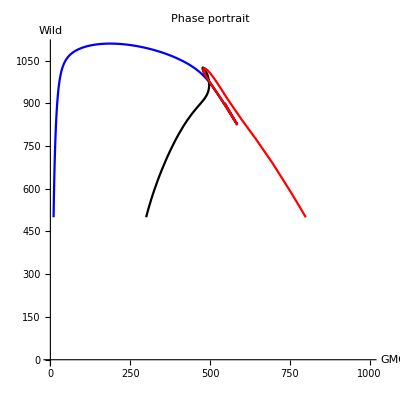

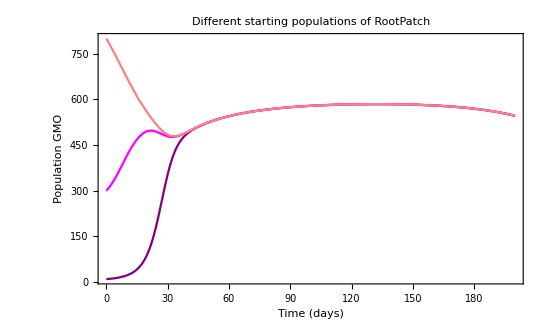

```mathematica
scen1={a0->0.5, b0->0.4,k->0.01,d1->0.05,s->0.001};
sol1=NDSolveValue[{all,init1}/.scen1,{G[t],M[t],B[t],A[t]},{t,0,200}];
sol2=NDSolveValue[{all,init2}/.scen1,{G[t],M[t],B[t],A[t]},{t,0,200}];
sol3=NDSolveValue[{all,init3}/.scen1,{G[t],M[t],B[t],A[t]},{t,0,200}];
Show[ParametricPlot[{{sol1[[1]],sol1[[3]]},{sol2[[1]],sol2[[3]]},{sol3[[1]],sol3[[3]]}},{t,0,200},PlotRange->{{0,1000},{0,1100}},PlotStyle->{Blue,Black,Red},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"GMO","Wild"}],StreamPlot [{GMO,Wild},{G,0,20},{B,0,4},StreamScale->{Tiny,Automatic,10}, StreamStyle->Pink]]
Plot[{sol1[[1]],sol2[[1]],sol3[[1]]},{t,0,200},AxesLabel->{"t","N"},PlotStyle->{Purple,Magenta,Pink},PlotRange->Full,PlotLabel->Style["Different starting populations of RootPatch",FontSize->20],Frame->{True,True,False,False},FrameLabel->{Style["Time (days)",FontSize->14],Style["Population GMO",FontSize->14]},FrameTicksStyle->Directive[FontSize->16]]
```